{a→0.0000239786,b→6.44857}

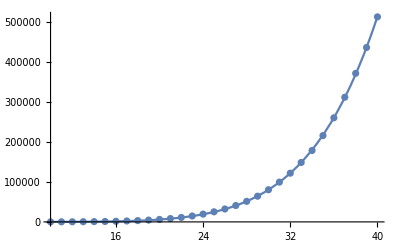

```mathematica
(* Vary Energy *)
x=Range[10,40];
y={116,186,293,460,706,1049,1590,2297,3261,4520,6170,8342,11157,14796,19471,25219,32287,40921,51419,64301,80421,99476,121851,148587,178643,215834,260320,311748,371498,436206,512821};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```

{a→0.023922,b→5.39628}

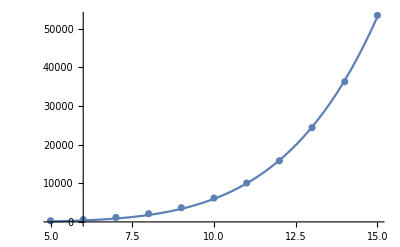

```mathematica
(* Vary system size *)
x=Range[5,15];
y={297,599,1151,2112,3666,6170,10061,15799,24380,36254,53413};
data = Transpose[{x,y}];
fit=FindFit[data,a*z^b,{a,b},z]
Show[Plot[a*z^b/.fit,{z,Min[x],Max[x]}],ListPlot[data]]
```